```mathematica
cost[cost_, rate_, mul_, pay_] = rate * mul * pay - cost;
DensityPlot3D[costbound[c, 0.05, m, p], {c, 0.01, 1.},{m, 1, 100}, {p, 0.01, 1.0}, AxesLabel->{"cost", "multiplier", "payment"}, PlotLegends->Automatic, PlotRange->{All, All, All, {-1,0}}, OpacityFunction->None]
```

-Graphics3D-

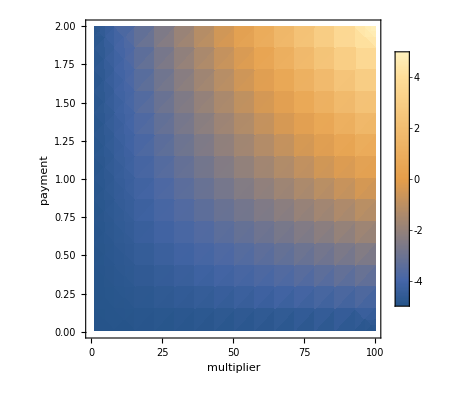

```mathematica
DensityPlot[costbound[5, 0.05, m, p],{m, 1, 100}, {p, 0.01, 2.0}, FrameLabel->{"multiplier", "payment"}, PlotLegends->Automatic, PlotRange->{-10,10}]
```